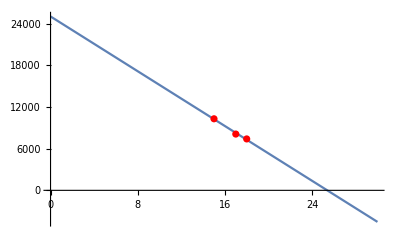

{158877.,{price→12.6957}}

```mathematica
salesdata = {
{15,10300},
{17,8100},
{18,7400}
};

(*Sales as a function of price*)
sales = Fit[
salesdata,{1,x},x];

Show[
Plot[Function[sales][x],{x,0,30}],
ListPlot[salesdata,PlotStyle->Red]
]

(*Revenue*)
NMaximize[
{
(25028.57142857151-985.7142857142902 price)*price,
price>1
},
price
]
```

```mathematica
localrevdata
```

```mathematica
(*Total revenue as a function of local revenue*)
factor := 1300000/133200.0 (*9.75975975975976*)
totalsales := 1300000/18.0
```

```mathematica
salesfactor := totalsales / 7400
```

```mathematica
{
(totalsales)*18.0(*Revenue*)
-80000*(5)(*Production costs*)
-940000(*fix costs*)
}
```

```mathematica
(*Maximize profit*)
NMaximize[
{
revenue 
- costs
,machine∈Integers,
0≤machine≤1,
price > 0
},
{
price,quant,machine
}
]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{1.32894×10^16,{price→16295.8,quant→-2.65839×10^15,machine→0}}